# Real Analysis, Lecture #20

## A Fundamental Result in Calculus: The Mean Value Theorem ("MVT")

### Statement of the MVT: If f is a continuous function on the closed interval [a,b] and a differentiable function on the open interval (a,b), then there exists a number c ∈ (a,b) such that f^′(c)=(f(b) - f(a))/(b - a)

### illustrating the theorem:

For the function f(x)=x^2 over an interval [a,b].

```mathematica
f[x_]:=x^2;Manipulate[Show[Plot[{f[x],((f[b]-f[a])/(b-a))*(x-a)+f[a],f'[(a+b)/2]*(x-(a+b)/2)+f[(a+b)/2]},{x,-4,4},PlotRange->{-5,15},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Green}}],ListPlot[{{a,f[a]},{b,f[b]},{(a+b)/2,f[(a+b)/2]},{a,0},{b,0},{(a+b)/2,0}},PlotStyle->PointSize[.02]],AxesLabel->{"x","y"}],{a,-3,b-.01},{b,-2.9,3}]
```

For an "arbitrary" differentiable function f over an interval [a,b] (the following code does not work perfectly because FindRoot is not guaranteed to find a c between a and b (it might find a c outside this interval), though it probably will for most examples):

```mathematica
f[x_]:=Cos[2x]-3x;Manipulate[sol=FindRoot[f'[c]==(f[b]-f[a])/(b-a),{c,(a+b)/2}];Show[Plot[{f[x],((f[b]-f[a])/(b-a))*(x-a)+f[a],f'[c/.sol]*(x-c/.sol)+f[c/.sol]},{x,-4,4},PlotRange->{-10,10},PlotStyle->{{Thick,Red},{Thick,Blue},{Thick,Green}}],ListPlot[{{a,f[a]},{b,f[b]},{c/.sol,f[c/.sol]},{a,0},{b,0},{c/.sol,0}},PlotStyle->PointSize[.02]],AxesLabel->{"x","y"}],{a,-3,b-.01},{b,-2.9,3}]
```

### Important consequences ("corollaries") of the theorem:

#### The Increasing Function Theorem: If f is a continuous function on the closed interval [a,b] and a differentiable function on the open interval (a,b) and if f^′(x)>0 for all x in the open interval (a,b), then f is a strictly increasing function on the closed interval [a,b]. (Note: there is a "Decreasing Function Theorem" too).

Warning:  you need to be careful in how you interpret this theorem.  Somewhat counter-intuitively, just because f^′(c)>0 at some number c, that does not mean that f is increasing for all x near c.  Consider the example below.

#### Example for Warning above

```mathematica
f[x_]:=If[x≠0,x/2+x^2*Sin[1/x],0]
```

```mathematica
Limit[(f[a]-f[0])/(a-0),a->0]
```

```mathematica
Manipulate[Plot[f[x],{x,-a,a},PlotRange->{-2a,2a},AxesLabel->{"x","y"},PlotStyle->Thick],{a,1,.01,-.01}]
```

```mathematica
Manipulate[Plot[f[x],{x,-a,a},PlotRange->{-a/20,a/20},AxesLabel->{"x","y"},PlotStyle->Thick],{a,1,.5,-.01}]
```

```mathematica
Manipulate[Show[Plot[f[x],{x,-a+.01,a+.01},PlotRange->{-a+f[.01],a+f[.01]},AxesLabel->{"x","y"},PlotStyle->Thick],ListPlot[{{.01,f[.01]}},PlotStyle->{PointSize[.02],Black}]],{a,1,.0001,-.0001}]
```

```mathematica
f'[.01]
```

```mathematica
Plot[f'[x],{x,-1,1},AxesLabel->{"x","y"}]
```

#### The Constant Function Theorem: If f is a continuous function on the closed interval [a,b] and a differentiable function on the open interval (a,b) and if f^′(x)=0 for all x in the open interval (a,b), then f is a constant on the closed interval [a,b].

#### Antiderivatives of the same function differ by constants: Let f and g be two functions which are continuous on the closed interval [a,b] and differentiable on the open interval (a,b). If f^′(x)=g^′(x) for all x in the open interval (a,b), then there is a constant C such that f(x)=g(x)+C for all x in the closed interval [a,b].

#### Other applications: (1) the first derivative test, (2) y=a ⅇ^(b x) is the "general solution" of the differential equation y^′=b y. Also, this function is the unique solution of the "initial value problem" y^′=b y, y(0)=a. (3) y=a cos(k x)+b sin(k x) is the "general solution" of the differential equation y^″=-k^2y. Also, this function is the unique solution of the initial value problem y^″=-k^2y, y(0)=a, y'(0) = b k. (4) The Fundamental Theorem of Calculus. And the list goes on and on and on...

### Idea of Proof of the Theorem (if we "Work Backwards")

#### It can be derived from Rolle's Theorem: If f is a continuous function on the closed interval [a,b] and a differentiable function on the open interval (a,b) and if f(a)=f(b), then there exists a number c ∈ (a,b) such that f^′(c)=0.

The MVT for a given function f and given interval [a,b] follows by applying Rolle's Theorem to the function g(x)=f(x)-L(x), where L(x)=(f(b)-f(a))/(b-a)(x-a)+f(a) is the function whose graph is the secant line to the graph of f between the points (a,f(a)) and (b,f(b)).

#### ...which can be derived from Fermat's Theorem (not to be confused with Fermat's Last Theorem or Fermat's Little Theorem): If c is a local extreme point (a local max or a local min) of a function f over an open interval (a,b), then either f is not differentiable at c or f^′(c)=0.

For a given function f and a given interval [a,b], Rolle's theorem follows from Fermat's theorem because of the following:

#### The Extreme Value Theorem (EVT): If f is a continuous function on the closed interval [a,b], then f has a global maximum and global minimum value on this interval. That is, in this situation there exist numbers c and d in the closed interval [a,b] such that f(c)≤f(x)≤f(d) for all x∈[a,b].

The truth of Fermat's Theorem follows from the definition of the derivative (which is based on the limit concept) and the definition of a local extreme point.  The truth of the EVT depends on a number of foundational ideas for our course.  They are:

#### The Definition of Continuity: A function f defined on an interval containing a number c is said to be continuous at c if for all ϵ>0, there exists a number δ>0 such that |f(x)-f(c)|<ϵ for all x in the interval which satisfy the condition that 0<|x-c|<ϵ. A function f is said to be continuous on an interval if it is continuous at every point in that interval. In effect, continuity at a number c says that lim_(x→c) f(x)=f(c) (assuming x is close enough to c to be in the domain of f ). In other words, the definition of continuity is inextricably linked to the concept of limits.

#### The Definition of Convergence of a Sequence: A sequence {x_n} is said to converge to a number L if for all ϵ>0, there exists a positive integer N such that |x_n-L|<ϵ for all positive integers n satisfying the condition that n≥N.

#### The Definition of a Bounded Sequence: A sequence {x_n} is bounded if there exists a number M>0 such that |x_n|<M for all positive integers n.

#### The Definition of a Subsequence of a Given Sequence: A subsequence of a given sequence {x_n} is a sequence made up of some of the terms of {x_n} in the same order they appear in the original sequence. To be more precise, a subsequence of {x_n} is any sequence that takes the form {x_p_n}, where {p_n} is a strictly increasing sequence of positive integers.

#### The (simplest form of the) Bolzano-Weierstrass Theorem: Every bounded sequence of real numbers has a convergent subsequence. Moreover, if {x_n} is a sequence of real numbers from the closed interval [a,b], then {x_n} has a subsequence {x_p_n} that converges to a real number in [a,b].

All of these things, in turn, are dependent on the Completeness Axiom (also called the Least Upper Bound Property).  This property is the most important property that distinguishes the field of real numbers ℝ from the field of rational numbers ℚ.

#### Completeness Axiom: For every nonempty set of real numbers which is bounded above, there exists a real number which is the least upper bound for that set. (that is, there is a smallest upper bound for the set).

Every nonempty set of rational numbers which is bounded above also has a least upper bound (since every rational number is a real number).  However, this least upper bound need not be a rational number!  In all likelihood, the least upper bound of a randomly chosen bounded set of rational numbers will be an irrational number (more on this when we get to section 1.4 of the textbook).

## Definition of Riemann Integrability

## Proof that a Function is Riemann Integrable

## Basic Properties

## Unbounded Functions are Not Riemann Integrable (Note: the existence of improper integrals of certain unbounded functions does not contradict this fact)

```mathematica
∫_0^1 1/Sqrt[x]ⅆx
```

## Equivalent Condition for Riemann Integrability

## Continuous Functions f:[a,b]⟶ℝ are Riemann Integrable

## Monotone Functions f:[a,b]⟶ℝ are Riemann Integrable

## The Oscillation of a Bounded Function over a Closed Interval (Notation Used: ω(f,[a,b]))

## Properties of Integrals

## The Fundamental Theorem of Calculus (FTC)

```mathematica
∫E^(-x^2)ⅆx
```

1/2 √π Erf[x]

```mathematica
Kinney[x_]:=NIntegrate[Sin[t^3+E^(t)]*Cos[t],{t,0,x}]
```

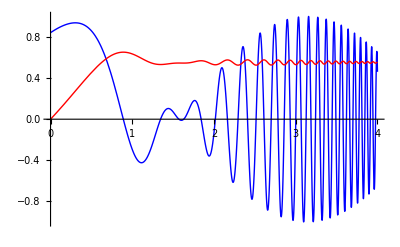

```mathematica
Plot[{Sin[x^3+E^(x)]*Cos[x],Kinney[x]},{x,0,4},PlotStyle->{{Thick,Blue},{Thick,Red}}]
```

```mathematica
D[(1/2)x*Sqrt[1-x^2]+(1/2)ArcSin[x],x]//Simplify
```

√(1-x^2)